```mathematica
PDF[VoigtDistribution[δ,σ],x]
```

(ⅇ^((-ⅈ x+δ)^2/(2 σ^2)) Erfc[(-ⅈ x+δ)/(√2 σ)]+ⅇ^((ⅈ x+δ)^2/(2 σ^2)) Erfc[(ⅈ x+δ)/(√2 σ)])/(2 √(2 π) σ)

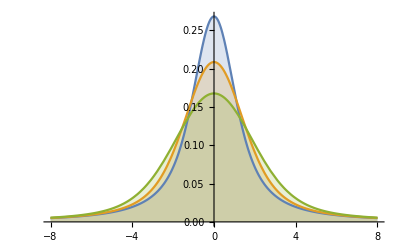

```mathematica
Plot[Table[PDF[VoigtDistribution[1,σ],x],{σ,{0.5,1.,1.5}}]//Evaluate,{x,-8,8},Exclusions->None,Filling->Axis]
```

```mathematica
skewedVoigt[μ_,δ_,σ_,skew_,x_]:=PDF[VoigtDistribution[δ,σ],(x-μ)]*(1+Erf[(skew(x-μ))/(σ √2)])
```

FindMaximum[skewedVoigt[0,1.5,1,-4,x],x]

((1+Erf[(skew (x-μ))/(√2 σ)]) (ⅇ^((δ-ⅈ (x-μ))^2/(2 σ^2)) Erfc[(δ-ⅈ (x-μ))/(√2 σ)]+ⅇ^((δ+ⅈ (x-μ))^2/(2 σ^2)) Erfc[(δ+ⅈ (x-μ))/(√2 σ)]))/(2 √(2 π) σ)

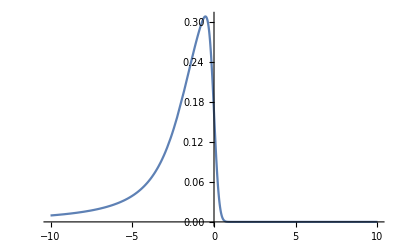

{0.30779,{x→-0.526447}}

```mathematica
skewedVoigt[μ,δ,σ,skew,x]
Plot[skewedVoigt[0,1.5,1,-4,x],{x,-10,10},PlotRange->All]
FindMaximum[skewedVoigt[0,1.5,1,-4,x],x]
```

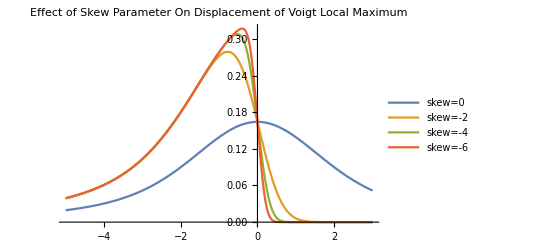

```mathematica
Plot[Table[skewedVoigt[0,1.5,1,skew,x],{skew,{0,-2,-4,-6}}]//Evaluate,{x,-5,3},PlotRange->All,PlotLegends->{"skew=0","skew=-2","skew=-4","skew=-6"},PlotLabel->"Effect of Skew Parameter On Displacement of Voigt Local Maximum"]
```

```mathematica
smooth[lis_,w_]:=(t=1/(∑_(i=-w)^w 1/(Abs[i]+1))Table[1/(Abs[i]+1)*lis[[1+w+i;;-1-(w-i)]],{i,-w,w}];
smoothedLis=∑_(i=1)^(2*w+1) t[[i]])
findXMax[dSet_]:=(xdat=dSet[[All,1]];
ydat=dSet[[All,2]];
posit=Position[ydat,Max[ydat]][[1,1]];
xdat[[posit]])

(*sampleLocalMax[hList_,nSamp_,res_,smoothWidth_]:=(
rSamp=RandomSample[hList,nSamp];
{xSample,ySample}=HistogramList[rSamp,{res}];
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findXMax[smoothData],smoothData})*)
sampleLocalMax[wList_,fList_,nSamp_,res_,smoothWidth_]:=(
rSamp=RandomChoice[wList->fList,nSamp];
{xSample,ySample}=HistogramList[rSamp,{res}];
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findXMax[smoothData],smoothData})

sampleLocalMax2[wList_,fList_,nSamp_,res_,smoothWidths_]:=(
rSamp=RandomChoice[wList->fList,nSamp];
{xSample,ySample}=HistogramList[rSamp,{res}];
smoothDatasets=Table[(
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findXMax[smoothData],smoothData}),{smoothWidth,smoothWidths}])

SubSampleDistMaker[wList_,fList_,nPoints_,res_,smoothingW_,n_]:=Table[sampleLocalMax[wList,fList,nPoints,res,smoothingW][[1]],{i,1,n}]
SubSampleDistMaker2[wList_,fList_,nPoints_,res_,smoothingWs_,n_]:=Table[sampleLocalMax2[wList,fList,nPoints,res,smoothingWs][[All,1]],{i,1,n}]

(*intFunc[func_,k1_,k2_]:=NIntegrate[N[func[x]],{x,k1,k2}]
intFunc[f,13280,13280.1]
6.012278942190535*)
(*interpF=ListInterpolation[weights,freqs]
integrolate[f_]:=Integrate[interpF[x],{x,f-.005,f+.005}]
integrolate[13281]*)
```

```mathematica
(*Now let's use more realistic subsample sizes*)
const=47.703;
μ0=13284.8704;Γ0=1.872;σ0=0.852;skew0=-4; amp0=259.59;
μ1=13278.6702;Γ1=1.938;σ1=0.640;skew1=-3.14;amp1=124.81;
μ2=13272.6024;Γ2=2.242;σ2=0.263;skew2=-1.03;amp2=68.54;
f[x_]:=amp0*skewedVoigt[μ0,Γ0,σ0,skew0,x]+amp1*skewedVoigt[μ1,Γ1,σ1,skew1,x]+amp2*skewedVoigt[μ2,Γ2,σ2,skew2,x]+const
f[x];
nmax= NMaximize[f[x],{x,13283,13286}][[2]];xMax=x/.nmax
 yMax=f[xMax]
```

13284.4

120.24

```mathematica
xMax
```

13284.4

```mathematica
13284.389253652711(*idk why I can't get Mathematica to print out the full thing*)
```

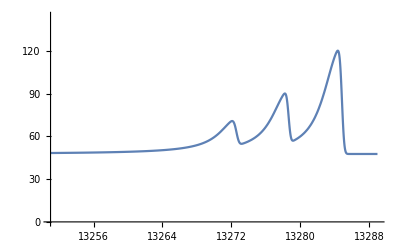

```mathematica
Plot[f[x],{x,13251,13289},PlotRange->{{13251,13289},{0,1.2*yMax}}]
```

```mathematica
(*tList=Flatten[Table[ConstantArray[x,Round[300*f[x]+300]],{x,13251,13289,.001}]];
Histogram[tList,{.001}]
Length[tList]
tsub=RandomSample[tList,413663];Histogram[tsub,{.01}]*)
```

```mathematica
res=0.001;
freqs=Table[k,{k,13251,13289,res}];
weights=Table[f[k],{k,13251,13289,res}];
(*weights=Map[f,freqs]*)
```

```mathematica
tSamp=RandomChoice[weights->freqs,413663];
```

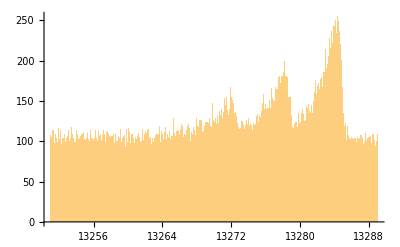

```mathematica
Histogram[tSamp,{.01}]
```

```mathematica
Timing[subsampCollection=SubSampleDistMaker[weights,freqs,413663,.01,3,1000];]
```

$Aborted

DataDistribution[…]

13284.3

0.131362

{13284.,13284.6}

{13284.2,13284.5}

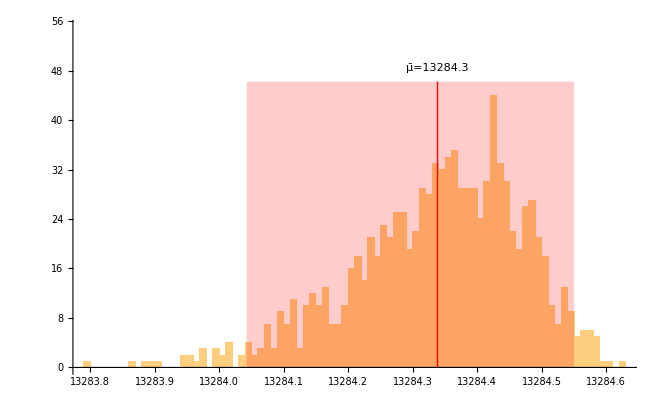

```mathematica
{hllistx,hlisty}=HistogramList[subsampCollection,{.01}];
ℋ=HistogramDistribution[subsampCollection,{.01}]
μBar=Moment[ℋ,1]
σBar=√Cumulant[ℋ,2]
{p951,p952}={Quantile[ℋ,0.025],Quantile[ℋ,0.975]}
{p681,p682}={Quantile[ℋ,0.32/2],Quantile[ℋ,1-0.32/2]}
Histogram[subsampCollection,{.01},Epilog->{Red,Line[{{μBar,0},{μBar,Max[hlisty]*1.05}}],Black,Text["μ̄="<>ToString[μBar],{μBar,Max[hListy]*1.1}],Red,Opacity[0.2],Rectangle[{p951,0},{p952,Max[hlisty]*1.05}]},PlotRange->{0,1.25*Max[hListy]}]
```

```mathematica
μBar-xMax
```

-0.0508837

```mathematica
sampleLocalMax2[weights,freqs,413663,.01,{0,1,2,3,4}][[All,1]]
```

{13284.6,13284.,13284.3,13284.3,13284.3}

```mathematica
Timing[μcoll=SubSampleDistMaker[weights,freqs,413663,.01,3,100];]
```

{14.6719,Null}

```mathematica
Timing[subsampCollections=SubSampleDistMaker2[weights,freqs,413663,.01,{0,1,2,3,4,5},100];](*Only took ~twice as long as with single smoothing setting, bc generating rand subsamples is a lot of the computation*)
```

{31.0781,Null}

```mathematica
Dimensions[subsampCollections]
```

{100,6}

```mathematica
Timing[subsampCollections=SubSampleDistMaker2[weights,freqs,413663,.01,{0,1,2,3,4,5},1000];]
```

{321.094,Null}

```mathematica
Length[subsampCollections[[All,6]]]
```

1000

```mathematica
xList=HistogramList[subsampCollections[[All,1]],{.01}][[1]];
yLists=Table[HistogramList[subsampCollections[[All,i]],{xList}][[2]],{i,1,6}];
Length[xList]
Length[yLists[[1]]]
```

118

117

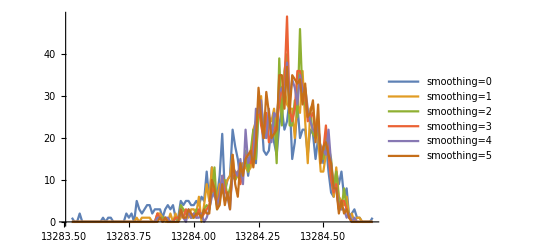

```mathematica
ListLinePlot[Table[Transpose[{xList[[;;-2]],yLists[[i]]}],{i,1,6}],PlotLegends->Table["smoothing="<>ToString[i],{i,0,5}]]
```

```mathematica
Timing[subsampCollections=SubSampleDistMaker2[weights,freqs,413663,.01,{0,2,5,10},10000];](*this is gonna take forever f...*)
```

{3542.91,Null}

```mathematica
nWidths=Dimensions[subsampCollections][[2]];
xList=HistogramList[subsampCollections[[All,1]],{.01}][[1]];
yLists=Table[HistogramList[subsampCollections[[All,i]],{xList}][[2]],{i,1,nWidths}];
Length[xList]
Length[yLists[[1]]]
```

150

149

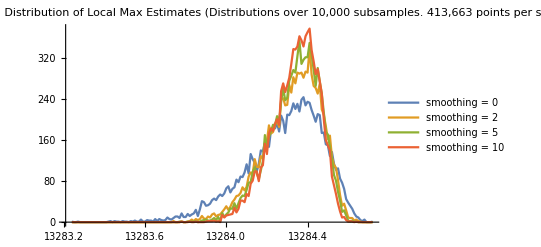

```mathematica
ListLinePlot[Table[Transpose[{xList[[;;-2]],yLists[[i]]}],{i,1,nWidths}],PlotLegends->Table["smoothing = "<>ToString[i],{i,{0,2,5,10}}],PlotLabel->Style["Effect of Smoothing Width on Distribution of Local Max Estimates\n (Distributions over 10,000 subsamples. 413,663 points per subsample)",18]]
```

```mathematica
ℋ5=HistogramDistribution[subsampCollections[[All,3]],{.01}];
μ5=Moment[ℋ5,1]
σ5=√Cumulant[ℋ5,2]
ℋ5CI95={Quantile[ℋ5,0.025],Quantile[ℋ5,0.975]}
ℋ5CI68={Quantile[ℋ5,0.32/2],Quantile[ℋ5,1-0.32/2]}
```

13284.3

0.124759

{13284.1,13284.5}

{13284.2,13284.5}

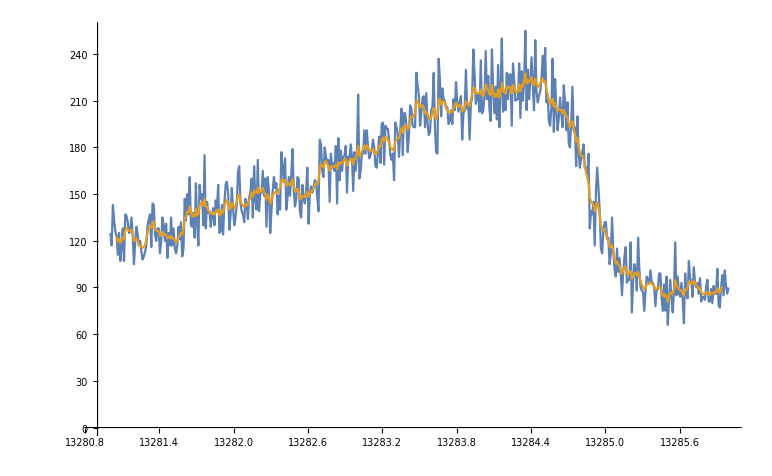

77619

```mathematica
{bins,counts}=HistogramList[tSamp,{Table[f,{f,13281,13286,.01}]}];
xSamp=smooth[(bins[[;;-2]]+bins[[2;;]])/2,0];ySamp=smooth[counts,0]; dSamp=Transpose[{xSamp,ySamp}];
xSamp5=smooth[(bins[[;;-2]]+bins[[2;;]])/2,5];ySamp5=smooth[counts,5]; dSamp5=Transpose[{xSamp5,ySamp5}];
ListLinePlot[{dSamp,dSamp5}]
counts=∑_(i=1)^Length[ySamp] ySamp[[i]]
```

```mathematica
FindPeaks[ySamp,20]
xSamp[[FindPeaks[ySamp,20][[All,1]]]]
```

{{343,254}}

{13284.4}

{4.07813,{x→13284.4}}

{4.03125,{x→13284.4}}

13284.4

222.646

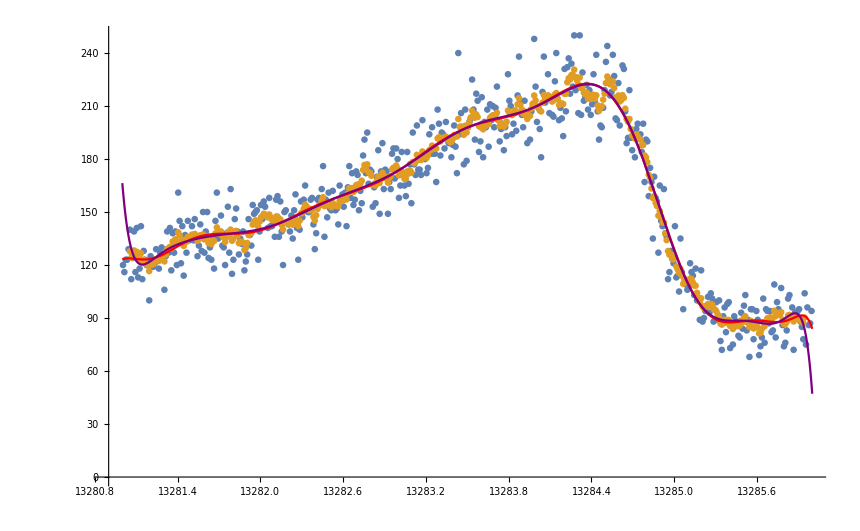

```mathematica
pollys=Table[(x-13284)^n,{n,0,16}];
pollys2=Table[(x-13284)^n,{n,0,16}];
fitFunc=Fit[dSamp,pollys,x];
fitFunc5=Fit[dSamp5,pollys2,x];
Timing[nmaxFit=NMaximize[{fitFunc,13283≤x≤13286},x,AccuracyGoal->3][[2]]]
Timing[nmaxFit2=NMaximize[{fitFunc5,13283≤x≤13286},x][[2]]]
xMaxFitFunc=x/.nmaxFit
yMaxFitFunc=fitFunc/.x->xMaxFitFunc

Show[{ListPlot[{dSamp,dSamp5}],Plot[{fitFunc,fitFunc5},{x,13281,13286},PlotStyle->{Red,Purple}]}]
```

```mathematica
Timing[NMaximize[{fitFunc,13283≤x≤13286},x]]
Timing[NMaximize[{fitFunc/.(x-13284)->x,-1≤x≤2},x]](*wow, check out how much faster it is if I just redefine my origin...*)
```

{4.54688,{222.646,{x→13284.4}}}

{0.1875,{222.646,{x→0.368165}}}

```mathematica
findPolyMax[dset_,p_,{guessLBound_,guessRBound_}]:=(
g=(guessLBound+guessRBound)/2;
pollys=Table[(x-g)^n,{n,0,p}];
fitFunc=Fit[dset,pollys,x];
nmaxFit=NMaximize[{fitFunc/.(x-g)->x,guessLBound-g≤x≤guessRBound-g},x][[2]];
xMaxFitFunc=(x/.nmaxFit)+g
(*{xMaxFitFunc}*)
)
sampleLocalMax3[wList_,fList_,nPoints_,{f1_,f2_,resolution_},smoothWidths_,p_,{guessLBound_,guessRBound_}]:=(
rSamp=RandomChoice[wList->fList,nPoints];
{xSample,ySample}=HistogramList[rSamp,{Table[f,{f,f1,f2,resolution}]}];
smoothDatasets=Table[(
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findPolyMax[smoothData,p,{guessLBound,guessRBound}],smoothData}),{smoothWidth,smoothWidths}])

SubSampleDistMaker3[wList_,fList_,nPoints_,{f1_,f2_,step_},smoothWidths_,p_,{guessLBound_,guessRBound_},n_]:=Table[sampleLocalMax3[wList,fList,nPoints,{f1,f2,step},smoothWidths,p,{guessLBound,guessRBound}][[All,1]],{i,1,n}]
(*l=1;m={1};
{Length[l],Length[{l}]}
{Length[Flatten[{l}]],Length[Flatten[{m}]]}
{0,1}
{1,1}*)
sampleLocalMax4[wList_,fList_,nPoints_,{f1_,f2_,resolution_},smoothWidth_,p_,{guessLBound_,guessRBound_}]:=(
Assert[smoothWidth∈Integers];
rSamp=RandomChoice[wList->fList,nPoints];
{xSample,ySample}=HistogramList[rSamp,{Table[f,{f,f1,f2,resolution}]}];
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findPolyMax[smoothData,p,{guessLBound,guessRBound}],smoothData})

SubSampleDistMaker4[wList_,fList_,nPoints_,{f1_,f2_,step_},smoothWidth_,p_,{guessLBound_,guessRBound_},n_]:=(
If[Length[Flatten[{smoothWidth}]]==1,Table[sampleLocalMax4[wList,fList,nPoints,{f1,f2,step},Flatten[{smoothWidth}][[1]],p,{guessLBound,guessRBound}][[1]],{i,1,n}],
Table[sampleLocalMax3[wList,fList,nPoints,{f1,f2,step},smoothWidth,p,{guessLBound,guessRBound}][[All,1]],{i,1,n}]])
```

```mathematica
Timing[fEsts=Table[findPolyMax[tSamp,b,13284.5,16{13281,13286,.01}],{b,{0,5,10,20}}];]
```

{0.,Null}

```mathematica
{bins,counts}=HistogramList[tSamp,{Table[f,{f,13281,13286,.01}]}];
xSamp=smooth[(bins[[;;-2]]+bins[[2;;]])/2,0];ySamp=smooth[counts,0]; dSamp=Transpose[{xSamp,ySamp}];counts0=∑_(i=1)^Length[ySamp] ySamp[[i]];
res=0.001;
freqs0=Table[k,{k,13281,13286,res}];weights0=Table[f[k],{k,13281,13286,res}];
```

```mathematica
Timing[fEsts=Table[sampleLocalMax3[weights0,freqs0,counts0,{13281,13286,.01},{0,5,10,20},p,{13284,13285}][[All,1]],{p,8,32,4}];]
```

{4.45313,Null}

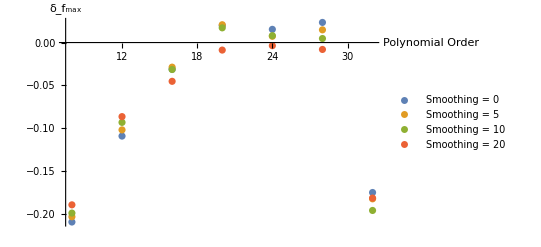

```mathematica
sWidths={0,5,10,20};polynomialOrders=Table[p,{p,8,32,4}];
(*ListPlot[Table[Transpose[{sWidths,fEsts[[i]]-xMax}],{i,1,Length[fEsts]}]]*)
ListPlot[Table[Transpose[{polynomialOrders,fEsts[[All,i]]-xMax}],{i,1,Length[sWidths]}],AxesLabel->{"Polynomial Order","δ_f_max"},PlotLegends->Table["Smoothing = "<>ToString[sWidths[[i]]],{i,1,Length[sWidths]}]]
```

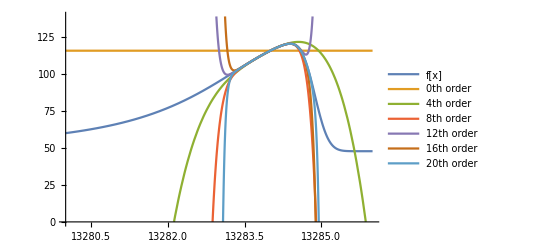

```mathematica
Plot[{f[x],Evaluate@Table[Normal@Series[f[x],{x,13284,n}],{n,0,20,4}]},{x,13280,13286},PlotRange->{0,f[13284]*1.2},PlotLegends->Flatten[{"f[x]",Table[ToString[n]<>"th order",{n,0,20,4}]}]]
```

```mathematica
pollys=Table[(x-13284)^n,{n,0,16}];
fitFunc=Fit[dSamp,pollys,x]
fitFunc2=LinearModelFit[dSamp,pollys,x]
fitFunc-fitFunc2["BestFit"]
resids=fitFunc2["StandardizedResiduals"];
rχsq=(∑_(i=1)^Length[resids] (resids[[i]])^2)/(Length[resids]-17)
```

209.91+38.356 (-13284+x)+45.7155 (-13284+x)^2-59.4535 (-13284+x)^3-261.599 (-13284+x)^4-65.2503 (-13284+x)^5+228.649 (-13284+x)^6+105.749 (-13284+x)^7-83.7465 (-13284+x)^8-52.341 (-13284+x)^9+12.288 (-13284+x)^10+11.7824 (-13284+x)^11+0.0600567 (-13284+x)^12-1.14026 (-13284+x)^13-0.150356 (-13284+x)^14+0.0284559 (-13284+x)^15+0.00525928 (-13284+x)^16

FittedModel[209.91+38.356 (-13284+x)+«20»+0.0284559 (-13284+x)^15+0.00525928 (-13284+x)^16]

0.

1.03112

```mathematica
redχ[data_,c_,p_]:=(
pollys=Table[(x-c)^n,{n,0,p}];
fitFunc=LinearModelFit[data,pollys,x,Weights->1/data[[All,2]]];
resids=fitFunc["FitResiduals"];
rχsq=(∑_(i=1)^Length[resids] (resids[[i]])^2/data[[i,2]])/(Length[resids]-(p+1)))
```

```mathematica
fitPlot[data_,c_,p_]:=(
xDat=data[[All,1]];
pollys=Table[(x-c)^n,{n,0,p}];
fitFunc=LinearModelFit[data,pollys,x,Weights->1/data[[All,2]]];
resids=fitFunc["FitResiduals"];
rχsq=(∑_(i=1)^Length[resids] (resids[[i]])^2/data[[i,2]])/(Length[resids]-(p+1));
data2=Table[{data[[i,1]],Around[data[[i,2]],√data[[i,2]]]},{i,1,Length[data]}];
Show[
{ListPlot[data2,PlotLabel->"p = "<>ToString[p]<>";  χ^2/((N_(d . o . f))_.) = "<>ToString[Round[rχsq,.001]]],Plot[Function[x,Evaluate[fitFunc["BestFit"]]][x],{x,Min[xDat],Max[xDat]},PlotStyle->Red]}] )
```

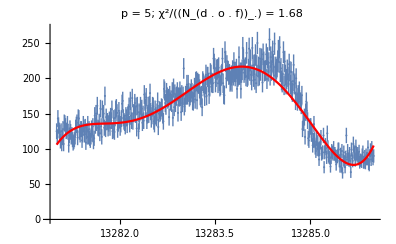
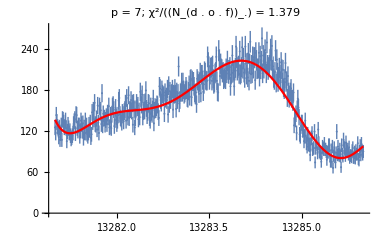
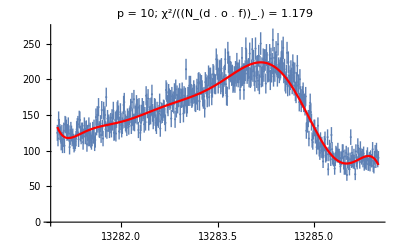
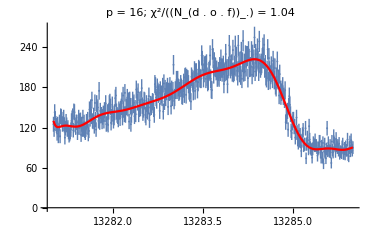

```mathematica
Table[fitPlot[dSamp,13284,p],{p,{5,7,10,16}}]
```

{{0,14.0825},{1,12.9758},{2,4.43055},{3,3.89004},{4,2.79849},{5,1.67969},{6,1.60189},{7,1.37918},{8,1.2256},{9,1.18901},{10,1.17893},{11,1.08198},{12,1.06319},{13,1.06127},{14,1.04865},{15,1.04334},{16,1.04003},{17,1.03393},{18,1.03449},{19,1.03319}}

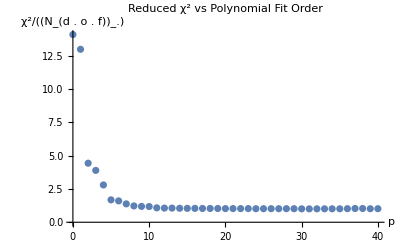

```mathematica
χvsPList=Table[{p,redχ[dSamp, 13284,p]},{p,0,40}];χvsPList[[1;;20]]
ListPlot[χvsPList,PlotRange->All,PlotLabel->"Reduced χ^2 vs Polynomial Fit Order",AxesLabel->{"p","χ^2/((N_(d . o . f))_.)"}]
```

```mathematica
Timing[μPolyEsts=SubSampleDistMaker4[weights0,freqs0,counts0,{13281,13286,.01},{5},16,{13284,13285},1000];]
```

{173.047,Null}

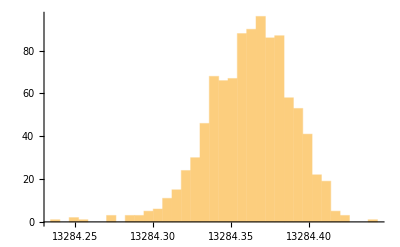

```mathematica
Histogram[μPolyEsts,{.006}]
```

```mathematica
ℋ5Poly0=HistogramDistribution[μPolyEsts,{.006}]
```

DataDistribution[…]

```mathematica
μPoly0=Moment[ℋ5Poly0,1]
δPoly0=μPoly0-xMax
σPoly0=√Cumulant[ℋ5Poly0,2]
```

13284.4

-0.0270636

0.0266889

```mathematica
Timing[μPolyEsts0=SubSampleDistMaker4[weights0,freqs0,counts0,{13281,13286,.01},0,16,{13284,13285},1000];]
```

{160.375,Null}

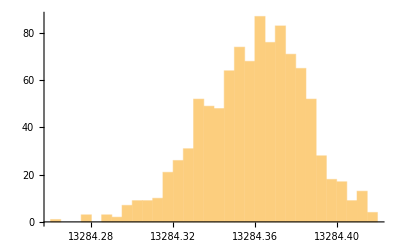

```mathematica
Histogram[μPolyEsts0,{.005}]
```

```mathematica
ℋ0Poly0=HistogramDistribution[μPolyEsts0,{.005}];
μ0Poly0=Moment[ℋ0Poly0,1]
δ0Poly0=μ0Poly0-xMax
σ0Poly0=√Cumulant[ℋ0Poly0,2]
```

13284.4

-0.0300186

0.0250629